```mathematica
ClearAll["Global`*"];
d=3;
nu=(d-2)/2;
CForLD[l_,d_]:=(-1)^l Pochhammer[2 nu,l]/(2^l Pochhammer[nu,l])
```

```mathematica
k[beta_,x_]:=x^(beta/2) Hypergeometric2F1[beta/2,beta/2,beta,x];
```

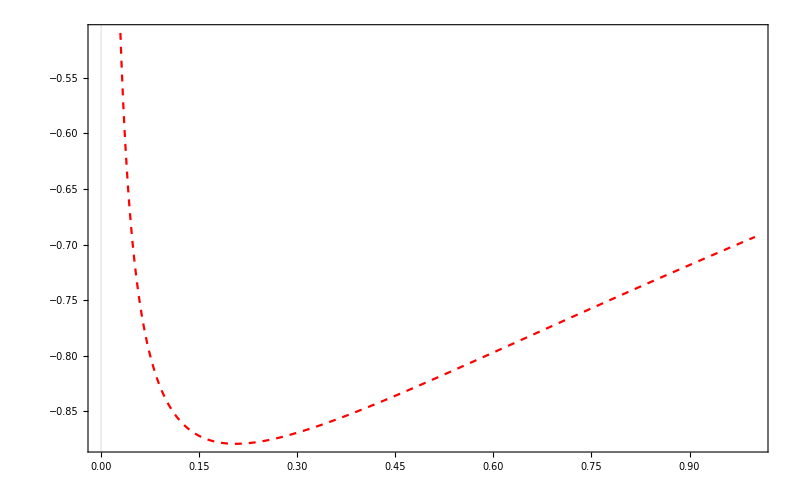

```mathematica
ConformalBlock2D[Delta_,l_,z_,zb_]:=CForLD[l,2]*((k[Delta+l,z]k[Delta-l,zb] )+   (k[Delta+l,zb]k[Delta-l,z]))/2;

Plot[ConformalBlock2D[Delta,1,z,zb]/.{zb->z}/.{z->1/2},{Delta,0,1},PlotTheme->"Scientific",PlotStyle->{Red,Dashed},ImageSize->800]
```

```mathematica
CoeffA[n_,j_,Delta_,l_]:=Module[{tau=Delta-(l+d-2)},

Return[(Zjl[j,l]CForLD[l,d]/CForLD[j,d-1])*((Pochhammer[(Delta+j)/2,n]Pochhammer[(tau+l+1-j)/2,n])/(Pochhammer[(Delta+j-1)/2,n]Pochhammer[(tau+l-j)/2,n]))*((Pochhammer[1/2,n]Pochhammer[Delta-1,2n]Pochhammer[(Delta+l)/2,n]Pochhammer[tau/2,n])/(16^n Factorial[n] Pochhammer[Delta-nu,n] Pochhammer[Delta-nu+n-1/2,n]Pochhammer[(Delta+l+1)/2,n]Pochhammer[(tau+1)/2,n]))
];
];
Zjl[j_,l_]:=Module[{p=(l-j)/2},
Return[(Pochhammer[1/2,p] Factorial[l] Pochhammer[nu,j+p] Pochhammer[2nu-1,j] (j+nu - (1/2)))/(Factorial[p]Factorial[j]Pochhammer[nu - 1/2 ,j+p+1]Pochhammer[2nu,l])];
]
```

```mathematica
SumTillN[N_,Delta_,l_,z_,zb_]:=Sum[Sum[CoeffA[n,j,Delta,l]ConformalBlock2D[Delta+2n,j,z,zb],{j,Mod[l,2],l}],{n,0,N}]
```

```mathematica
Table[SumTillN[N,Delta,1,0.5,0.5],{N,1,10}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

```mathematica
Limit[CoeffA[n,j,Delta,l],j->0]
```

$Aborted